```mathematica
xmin=-8; xmax=8;
sol=NDSolve[{D[u[x,t],t]==6u[x,t] D[u[x,t],x]-D[u[x,t],x,x,x],u[x,0]==-2 Sech[x]^2, u[xmin,t]==u[xmax,t]},u,{x,xmin,xmax},{t,-1,1}]
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

{{u→InterpolatingFunction[{{…, -8., 8., …}, {-1., 1.}}, <>]}}

```mathematica
Plot3D[u[x,t]/.Flatten[sol],{x,xmin,xmax},{t,-1,1},PlotPoints->50, PlotRange->All,AxesLabel->{"x","t","u"}]
```

-Graphics3D-

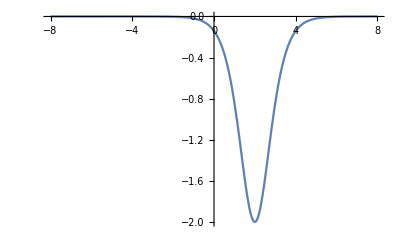

```mathematica
Plot[u[x,0.5]/.Flatten[sol],{x,xmin,xmax},PlotRange->All]
```

```mathematica
kdvData=Table[u[x,tt]/.Flatten[sol],{tt,-1,1, 0.01}];
```

```mathematica
ListPlot[kdvData]
```

ListPlot::lpn: TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]][x, tt], {tt, -1.`, 1.`, 0.01`} is not a list of numbers or pairs of numbers.

ListPlot[Data[InterpolatingFunction[{{…, -8., 8., …}, {-1., 1.}}, <>][x,tt],{tt,-1,1,0.01}]]